```mathematica
<<peeters` ;
peeters`setGitDir[ "blogit" ]
```

C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit

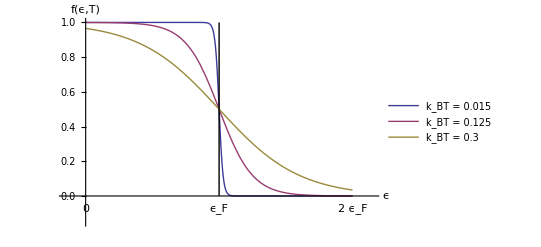

{C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/fermiDiracLevelCurvesFig1.eps,C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/fermiDiracLevelCurvesFig1pn.png}

```mathematica
Clear[ tl ] ;
tl = Module[ {fd, tauLevels, eMax},
fd[ e_, mu_, tau_] = (E^((e - mu)/tau) + 1)^(-1) ;
eMax = 2 ;
space = 0.15 ;
tauLevels = {0.015, 0.125, 0.3} ;
Plot[ 
Evaluate@Table[fd[e, 1, tau], {tau, tauLevels}]
, {e, 0, eMax} 
, Ticks -> { None, Automatic}
, AxesLabel -> { ϵ, f[ϵ, T]}
, Epilog -> { Table[ Text[r Subscript[ϵ, F], {r, -space/2}], {r, 0, eMax}], Line[{{1, 0}, {1, 1}}]}
,PlotRange->{{-space,eMax+space},{-space,1}}
, PlotLegends-> Placed[ Text[ "k_BT = "  <> ToString[#]] &/@tauLevels, {Right,Top} ]
]
]

(*peeters`exportForLatex["fermiDiracLevelCurvesFig1", tl]*)
```

```mathematica
Manipulate[
DynamicModule[ {fd, tauLevels,eMax},
fd[ e_, mu_, tau_] = (E^((e - mu)/tau) + 1)^(-1) ;
eMax = 2 (*mu*) ;
space = 0.15 ;
Plot[ 
fd[e, mu, tau]
, {e, 0, eMax} 
, PlotRange -> Full
, AxesLabel -> { ϵ, f[ϵ, T]}
]
] 
, { {mu, 1, μ}, 0, 4, Appearance->"Open"}
, {{tau, 0.015,"k_BT" }, 0.001, 4, Appearance->"Open"}
]
```

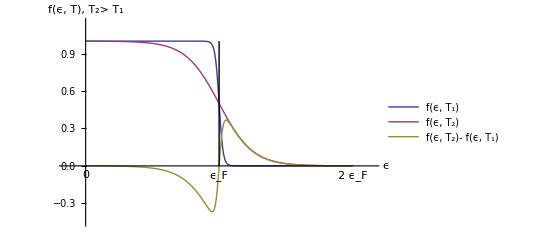

{C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/fermiDiracLevelCurvesFig2.eps,C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/fermiDiracLevelCurvesFig2pn.png}

```mathematica
Clear[ t2 ] ;
t2 = Module[ {fd, tauLevels, eMax, a},
fd[ e_, mu_, tau_] = (E^((e - mu)/tau) + 1)^(-1) ;
tauLevels = {0.015, 0.125} ;
a = {fd[e, 1, #] &/@ tauLevels, fd[ e, 1, tauLevels[[2]]]- fd[ e, 1, tauLevels[[1]]]} // Flatten ;
eMax = 2 ;
space = 0.15 ;

Plot[ 
Evaluate@a
, {e, 0, eMax} 
, Ticks -> { None, Automatic}
, AxesLabel -> { ϵ, "f(ϵ, T), T_2> T_1"}
, Epilog -> { 
Table[ Text[r Subscript[ϵ, F], {r, -space/2}], {r, 0, eMax}],
Line[{{1, 0}, {1, 1}}](*,
Text["μ = E_F", {1, 1}]*)
}
, PlotRange->{{-space,eMax+space},{-3space,1 + space}}
, PlotLegends-> Placed[ {
"f(ϵ, T_1)", "f(ϵ, T_2)", "f(ϵ, T_2)- f(ϵ, T_1)"
}, {Right,Top} ]
]
]

(*peeters`exportForLatex["fermiDiracLevelCurvesFig2", t2]*)
```

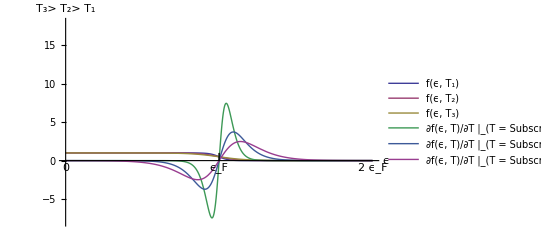

{C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/fermiDiracLevelCurvesAndDerivativesFig3.eps,C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/fermiDiracLevelCurvesAndDerivativesFig3pn.png}

```mathematica
Clear[ t3 ] ;
t3 = Module[ {fd, dfd, tauLevels, eMax, a},
fd[ e_, mu_, tau_] = (E^((e - mu)/tau) + 1)^(-1) ;
dfd[ e_, mu_, tau_ ] = D[ fd[e, mu, tau], tau] ;
tauLevels = {0.01, 0.02, 0.03}*3 ;
a = {fd[e, 1, #] &/@ tauLevels, dfd[e, 1, #] &/@ tauLevels} // Flatten ;
eMax = 2 ;
space = 0.15 ;

Plot[ 
Evaluate@a
, {e, 0, eMax} 
, Ticks -> { None, Automatic}
, AxesLabel -> { ϵ, "T_3> T_2> T_1"}
, Epilog -> { 
Table[ Text[r Subscript[ϵ, F], {r, -6 space}], {r, 0, eMax}],
Line[{{1, 0}, {1, 1}}]
}
, PlotRange -> { Full, {-8, 18}}
, PlotLegends->  Placed[{
"f(ϵ, T_1)", "f(ϵ, T_2)", "f(ϵ, T_3)", "∂f(ϵ, T)/∂T |_(T = SubscriptBox[T, 1])", "∂f(ϵ, T)/∂T |_(T = SubscriptBox[T, 2])", "∂f(ϵ, T)/∂T |_(T = SubscriptBox[T, 3])"
}, {Right, Top}]
]
]

(*peeters`exportForLatex["fermiDiracLevelCurvesAndDerivativesFig3", t3]*)
```

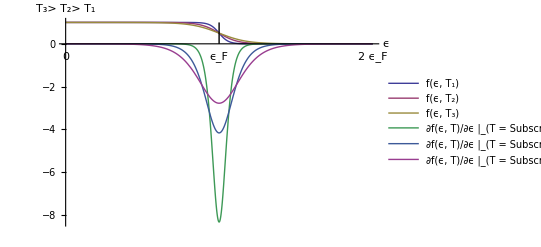

{C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/fermiDiracLevelCurvesAndEnergyDerivativesFig4.eps,C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/fermiDiracLevelCurvesAndEnergyDerivativesFig4pn.png}

```mathematica
Clear[ t4 ] ;
t4 = Module[ {fd, dfd, tauLevels, eMax, a},
fd[ e_, mu_, tau_] = (E^((e - mu)/tau) + 1)^(-1) ;
dfd[ e_, mu_, tau_ ] = D[ fd[e, mu, tau], e] ;
tauLevels = {0.01, 0.02, 0.03}*3 ;
a = {fd[e, 1, #] &/@ tauLevels, dfd[e, 1, #] &/@ tauLevels} // Flatten ;
eMax = 2 ;
space = 0.15 ;

Plot[ 
Evaluate@a
, {e, 0, eMax} 
, Ticks -> { None, Automatic}
, AxesLabel -> { ϵ, "T_3> T_2> T_1" }
, Epilog -> { 
Table[ Text[r Subscript[ϵ, F], {r, -4 space}], {r, 0, eMax}],
Line[{{1, 0}, {1, 1}}]
}
, PlotRange -> Full
, PlotLegends->  Placed[{
"f(ϵ, T_1)", "f(ϵ, T_2)", "f(ϵ, T_3)", "∂f(ϵ, T)/∂ϵ |_(T = SubscriptBox[T, 1])", "∂f(ϵ, T)/∂ϵ |_(T = SubscriptBox[T, 2])", "∂f(ϵ, T)/∂ϵ |_(T = SubscriptBox[T, 3])"
}, {Right,Bottom} ]
]
]

(*peeters`exportForLatex["fermiDiracLevelCurvesAndEnergyDerivativesFig4", t4]*)
```

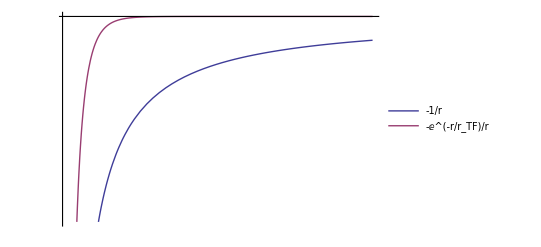

{C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/thomasFermiScreeningFig5.eps,C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/thomasFermiScreeningFig5pn.png}

```mathematica
Clear[t5]
t5 = Module[{a, f},
f[r_, rtf_] = -E^(- r/rtf)/r ;
a = f[r, #] &/@ {Infinity, 1/2 } ;

Plot[   Evaluate@a, {r, 0.1, 10}
, Ticks -> None
, PlotLegends->  Placed[ f[r, #] &/@ {Infinity, Subscript[r, TF] }, {Right,Bottom} ]
]
]

(*peeters`exportForLatex["thomasFermiScreeningFig5", t5]*)
```